```mathematica
Print["Initializing Minkowski Penrose Coordinates"];
Yright[ct_,r_,scale_]:=(Tanh[(ct+r)/scale]-Tanh[(ct-r)/scale])/2;
Yup[ct_,r_,scale_]:=(Tanh[(ct+r)/scale]+Tanh[(ct-r)/scale])/2;
PenroseptM[ct_,r_,scale_,size_,trans_] :=size*{Yright[ct,r,scale]+trans[[1]],Yup[ct,r,scale]+trans[[2]]};
```

Initializing Minkowski Penrose Coordinates

```mathematica
Print["Initializing all Schwarzschild Penrose Functions"];
ctout[ct_,r_]:=ct;
rout[ct_,r_]:=r+Rs*Log[r/Rs-1];
ctin[ct_,r_]:=r+Rs*Log[1-r/Rs];
rin[ct_,r_]:=ct;

Yrightin[ct_,r_,Schscale_]:=(Tanh[(ctin[ct,r]+rin[ct,r])/Schscale]-Tanh[(ctin[ct,r]-rin[ct,r])/Schscale])/2-1;
Yupin[ct_,r_,Schscale_]:=(Tanh[(ctin[ct,r]+rin[ct,r])/Schscale]+Tanh[(ctin[ct,r]-rin[ct,r])/Schscale])/2+1;
Yrightout[ct_,r_,Schscale_]:=(Tanh[(ctout[ct,r]+rout[ct,r])/Schscale]-Tanh[(ctout[ct,r]-rout[ct,r])/Schscale])/2;
Yupout[ct_,r_,Schscale_]:=(Tanh[(ctout[ct,r]+rout[ct,r])/Schscale]+Tanh[(ctout[ct,r]-rout[ct,r])/Schscale])/2;
Penroseptin[ct_,r_,Schscale_,size_,trans_] :=size*{Yrightin[ct,r,Schscale]+trans[[1]],Yupin[ct,r,Schscale]+trans[[2]]};
Penroseptout[ct_,r_,Schscale_,size_,trans_] :=size*{Yrightout[ct,r,Schscale]+trans[[1]],Yupout[ct,r,Schscale]+trans[[2]]};
Penrosept[ct_,r_,Schscale_,size_,trans_] := Which[
r≥ Rs,Penroseptout[ct,r,Schscale,size,trans],
True, Penroseptin[ct,r,Schscale,size,trans]
];

(**********)
Print["Initializing Schwarzschild Photon Trajectory Functions"];
OutgoingPhotonTimeout[r_,ro_]:=r-ro+Rs*Log[(r-Rs)/(ro-Rs)];
IngoingPhotonTimeout[r_,ro_]:=-(r-ro+Rs*Log[(r-Rs)/(ro-Rs)]);
OutgoingPhotonTimein[r_,ro_]:=r-ro+Rs*Log[Abs[(r-Rs)/(ro-Rs)]];
IngoingPhotonTimein[r_,ro_]:=-(r-ro+Rs*Log[Abs[(r-Rs)/(ro-Rs)]]);
OutgoingPhotonTime[r_,ro_]  := Which[
r≥ Rs, OutgoingPhotonTimeout[r,ro],
True, OutgoingPhotonTimein[r,ro]
];
IngoingPhotonTime[r_,ro_]  := Which[
r≥ Rs, IngoingPhotonTimeout[r,ro],
True, IngoingPhotonTimein[r,ro]
];

LightOut[ro_,rf_]:=ParametricPlot[{r,OutgoingPhotonTime[r,ro]},{r,ro,rf}];
LightIn[ro_,rf_]:=ParametricPlot[{r,IngoingPhotonTime[r,ro]},{r,ro,rf}];

Penroselightoutgoing[ro_,rf_,Schscale_,size_,trans_]:=ParametricPlot[Penrosept[OutgoingPhotonTime[r,ro],r,Schscale,size,trans],{r,ro,rf}];
Penroselightingoing[ro_,rf_,Schscale_,size_,trans_]:=ParametricPlot[Penrosept[IngoingPhotonTime[r,ro],r,Schscale,size,trans],{r,ro,rf}];
```

Initializing all Schwarzschild Penrose Functions

Initializing Schwarzschild Photon Trajectory Functions

```mathematica
Print["Construction of Schwarzschild Penrose Diagram with Photon Trajectory"];
Rs=10;
pltrin = ParametricPlot[Table[Penrosept[tt,n,5,1,{0,0}],{n,0,10}],{tt,-70,80},PlotRange->All,PlotStyle->Blue, Axes->False];
pltrout = ParametricPlot[Table[Penrosept[tt,0.1n,5,1,{0,0}],{n,101,160}],{tt,-70,70},PlotRange->All,PlotStyle->Blue, Axes->False];
pltt= ParametricPlot[Table[Penrosept[nn,rr,5,1,{0,0}],{nn,-30,30}],{rr,0.0000000001,40},PlotRange->All,Axes->False,PlotStyle->Black];
```

Construction of Schwarzschild Penrose Diagram with Photon Trajectory

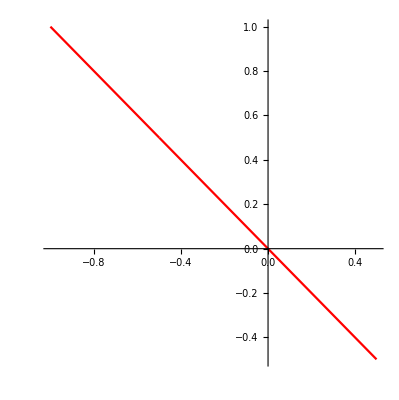

```mathematica
Initialpoint = ro/. FindRoot[IngoingPhotonTime[0,ro]==0,{ro,12.5}];
Schphoton = ParametricPlot[Penrosept[IngoingPhotonTime[r,Initialpoint],r,5,1,{0,0}],{r,15,0.0001},PlotStyle->Red]
```

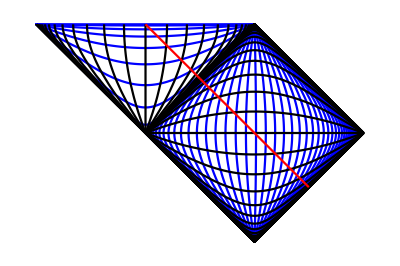

```mathematica
DiagramSch = Show[pltrin,pltrout,pltt, Schphoton]
```

```mathematica
Print["Rescaling and Translating Minkowski Penrose Diagram with Photon Trajectory"];
rmax =20;
SZ = 3;
trans = {-1,1};
plt2r = ParametricPlot[Table[PenroseptM[t,rj,5,SZ,trans/SZ],{rj,0,rmax}],{t,-rmax,rmax},PlotStyle->Gray];
plt2t = ParametricPlot[Table[PenroseptM[tj,r,5,SZ,trans/SZ],{tj,-rmax,rmax}],{r,0,rmax},PlotStyle->Yellow];
photon = ParametricPlot[PenroseptM[t,-t,5,SZ,trans/SZ],{t,-rmax,0}, PlotStyle-> Black];
Diagram = Show[plt2r,plt2t,photon];
```

Rescaling and Translating Minkowski Penrose Diagram with Photon Trajectory

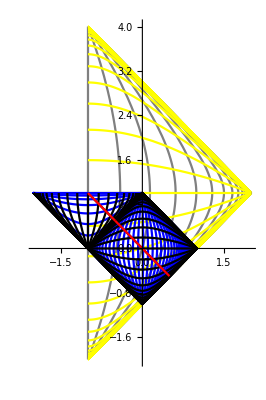

```mathematica
Show[Diagram, DiagramSch, PlotRange->All]
```

```mathematica
(***Cutoff Minkowski and Schwarzschild***)
```

```mathematica
Print["Rescaling and Translating Minkowski Penrose Diagram with Photon Trajectory"];
rmax =20;
SZ = 3;
trans = {-1,1};
rboundary = Rs;
tboundary = -rboundary;
MkScale = Msc/. FindRoot[PenroseptM[tboundary,rboundary,Msc,SZ,trans/SZ][[1]]==-0.5, {Msc,3}];
plt2r = Table[ParametricPlot[PenroseptM[t,rj,MkScale,SZ,trans/SZ],{t,-rmax,-rj},PlotStyle->Gray],{rj,0,rmax-1}];
plt2t = Table[ParametricPlot[PenroseptM[tj,r,MkScale,SZ,trans/SZ],{r,0,-tj},PlotStyle->Yellow],{tj,-rmax,-1}];
photon = ParametricPlot[PenroseptM[t,-t,MkScale,SZ,trans/SZ],{t,-0.8*rmax,0}, PlotStyle-> Black];
Diagram2 = Show[plt2r,plt2t,photon];
```

Rescaling and Translating Minkowski Penrose Diagram with Photon Trajectory

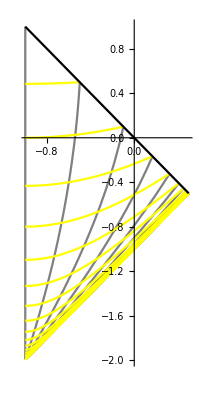

```mathematica
TestM= Show[Diagram2, PlotRange->All]
```

```mathematica
Print["Rescaling and Translating Schwarzschild Penrose Diagram with Photon Trajectory"];
rmax =20;
SZ = 3;
trans = {-1,1};
plt2r = Table[ParametricPlot[PenroseptM[t,rj,5,SZ,trans/SZ],{t,-rmax,-rj},PlotStyle->Gray],{rj,0,rmax-1}];
plt2t = Table[ParametricPlot[PenroseptM[tj,r,5,SZ,trans/SZ],{r,0,-tj},PlotStyle->Yellow],{tj,-rmax,-1}];
photon = ParametricPlot[PenroseptM[t,-t,5,SZ,trans/SZ],{t,-0.8*rmax,0}, PlotStyle-> Black];
Diagram2 = Show[plt2r,plt2t,photon];
```

Rescaling and Translating Schwarzschild Penrose Diagram with Photon Trajectory

```mathematica
Rs=1;
SSz = 1;
r =2;
t = -r;
Schscale2 =SchSc /.FindRoot[Penrosept[IngoingPhotonTime[r,Initialpoint],r,SchSc,SSz,{0,0}][[1]]== PenroseptM[t,r,MkScale,SZ,trans/SZ][[1]],{SchSc,3}];
pltSr=Table[ParametricPlot[Penrosept[tt,rj+0.000001,Schscale2,SSz,{0,0}],{tt,IngoingPhotonTime[rj+0.000001,Initialpoint],rmax},PlotStyle->Gray],{rj,2,20}];
pltSt = Table[ParametricPlot[Penrosept[tj,rr,Schscale2,SSz,{0,0}],{rr,0,-tj},PlotStyle->Yellow],{tj,-rmax,-1}];
```

ParametricPlot::plln: Limiting value -2.-3.14159 ⅈ in {tt,IngoingPhotonTime[rj+1.×10^-6,Initialpoint],rmax} is not a machine-sized real number.

ParametricPlot::plln: Limiting value -3.69315-3.14159 ⅈ in {tt,IngoingPhotonTime[rj+1.×10^-6,Initialpoint],rmax} is not a machine-sized real number.

ParametricPlot::plln: Limiting value -5.09861-3.14159 ⅈ in {tt,IngoingPhotonTime[rj+1.×10^-6,Initialpoint],rmax} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

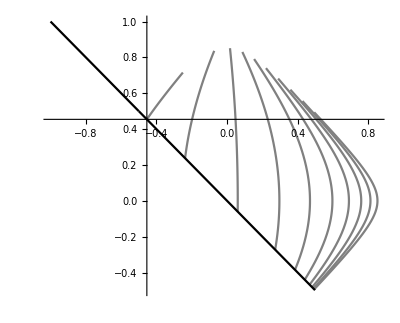

```mathematica
TestS =Show[pltSr,Schphoton1, PlotRange->All]
```

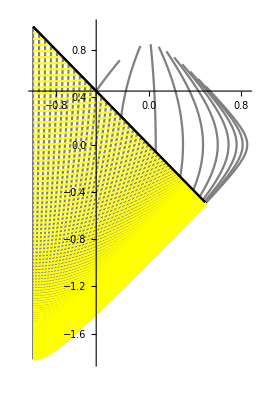

```mathematica
Show[TestS, TestM]
```